# Hemi-torus(HT)+wetting layer (WL) embeded in a rectangular matrix T.O. Cheche University of Bucharest September 2020

## 1. Zincblende crystal

1.1 Zincblende structure algorithm

How to build bulk zincblende structure
-Graphics-
Superpose the atom labels from the above squares and below cube.
-Graphics-

1.2 Zincblende structure
      Input:  a1, a2, nmax[2]

For given nmax[2], nmax[1] is chosen such as nmax[1]*a1 is closest possible of nmax[2]*a2 to ensure the same size of the two fcc structures (GaSb and GaAs, for example) in the xy plan.

```mathematica
a1=4.5 ;(*5.6533 for GaAs matrix - out*)
a2=6.;(*6.0583 for GaSb HT - in*)
nmax[2]=9; 
nmax[1]=IntegerPart[nmax[2]*a2/a1];
Print["nmax[1]*a1=",nmax[1]*a1,"; nmax[2]*a2=",nmax[2]*a2]
(**********************************************)
```

nmax[1]*a1=54.; nmax[2]*a2=54.

For below cells:
p[1, 1], p[2, 1], p[3, 1], p1[4, 1] define matrices associated to Ga or As atoms with iteration nmax[1];
p[1, 2], p[2, 2], p[3, 2], p1[4, 2]  define matrices associated to Ga or As atoms with iteration nmax[2];
p[ ...] represents an atom and has 4 elements, 3 for the atom position + 1 for the atom type.
The positions of atoms is defined in a fcc structure with lattice constant = 1.

**********************************************
For Ga:
m[1,..], m[2,..] are positions of Ga atoms in a layer with z=2k/2;
m[3,..], m[4,..] are positions of Ga atoms in a layer with z=(2k+1)/2.

```mathematica
p[1,1]={};p[2,1]={};p[3,1]={};p[4,1]={};(*for out*)
p[1,2]={};p[2,2]={};p[3,2]={};p[4,2]={};(*for out*)
m[1,i_,j_,k_]:=1/2*{2i,2j,2k,2};m[2,i_,j_,k_]:=1/2*{2i+1,2j-1,2k,2};
m[3,i_,j_,k_]:=1/2*{2i,2j+1,2k+1,2};m[4,i_,j_,k_]:=1/2*{2i+1,2j,2k+1,2};

Do[
Do[
Do[
n[t,q]=Append[m[t,i,j,k],p[t,q]];p[t,q]=n[t,q],
{i,-nmax[q],nmax[q]},{j,-nmax[q],nmax[q]},{k,-IntegerPart[nmax[q]/4],IntegerPart[nmax[q]/4]}];
p[t,q]=Partition[Flatten[p[t,q]],4],
{t,1,4}],
{q,1,2}];

Ga1=Partition[Flatten[Append[Append[Append[p[1,1],p[2,1]],p[3,1]],p[4,1]]],4] ;
Ga2=Partition[Flatten[Append[Append[Append[p[1,2],p[2,2]],p[3,2]],p[4,2]]],4];
Clear[m,n,p];
```

**********************************************
For As:
m[1,..], m[2,..] are positions of As atoms in a layer with z=(3+4k)/4;
m[3,..], m[4,..] are positions of As atoms in a layer with z=(1+4k)/4.

```mathematica
p[1,1]={};p[2,1]={};p[3,1]={};p[4,1]={};(*for out*)
p[1,2]={};p[2,2]={};p[3,2]={};p[4,2]={};(*for out*)
m[1,i_,j_,k_]:=1/4*{4i-1,4j+1,(3+4k),8};m[2,i_,j_,k_]:=1/4*{4i+1,4j-1,(3+4k),8};
m[3,i_,j_,k_]:=1/4*{4i+1,4j+1,(1+4k),8};m[4,i_,j_,k_]:=1/4*{4i+3,4j-1,(1+4k),8};

Do[
Do[
Do[
n[t,q]=Append[m[t,i,j,k],p[t,q]];p[t,q]=n[t,q],
{i,-nmax[q],nmax[q]},{j,-nmax[q],nmax[q]},{k,-IntegerPart[nmax[q]/4],IntegerPart[nmax[q]/4]}];
p[t,q]=Partition[Flatten[p[t,q]],4],
{t,1,4}],
{q,1,2}];

As1=Partition[Flatten[Append[Append[Append[p[1,1],p[2,1]],p[3,1]],p[4,1]]],4]; 
As2=Partition[Flatten[Append[Append[Append[p[1,2],p[2,2]],p[3,2]],p[4,2]]],4];
Clear[m,n,p];

dimAs1=Dimensions[As1][[1]];
AsPosition1=As1[[1;;dimAs1,1;;3]];

(*for in*)
dimAs2=Dimensions[As2][[1]];
AsPosition2=As2[[1;;dimAs2,1;;3]];
```

**********************************************
For Sb :

```mathematica
SbPosition2=AsPosition2; (*identical with As2*)
(* add a column of 3 for the atom type*)
column=Table[3,{i,1,dimAs2}];
Sb2=Join[SbPosition2,Partition[column,1],2] ;
```

1.3 HT+WL draw

```mathematica
Print["R0= ",R0=3*(a1+a2)/2, "A^o"];
Print["RQ= ",RQ=1.5*(a1+a2)/2, "A^o"];Tor=ParametricPlot3D[{Cos[t] (R0+RQ*Cos[u]),Sin[t] (R0+RQ*Cos[u]),RQ*Sin[u]},{t,0,2 Pi},{u,0, Pi},PlotStyle->Opacity[0.9]];
Plan1[x_,y_]:=0;
Plan2[x_,y_]:=-a1/3;
PLAN1=Plot3D[Plan1[x,y],{x,-(R0+3/2RQ),(R0+3/2RQ)},{y,-(R0+3/2RQ),(R0+3/2RQ)},PlotStyle->{Opacity[0.4]},PlotRange->All];
PLAN2=Plot3D[Plan2[x,y],{x,-(R0+3/2RQ),(R0+3/2RQ)},{y,-(R0+3/2RQ),(R0+3/2RQ)},PlotStyle->{Opacity[0.4]},PlotRange->All];
Show[Tor,PLAN1,PLAN2,BoxRatios->{1, 1, 1/4},PlotRange->All,Axes->False]
```

R0= 15.75A^o

RQ= 7.875A^o

-Graphics3D-

## 2. GaSb QD embeded in a GaAs matrix - run1.2 Skip 2.3&2.7 for HT+WL or 2.2&2.6 for Cone+WL

2.1 Input:  R0, RQ, Rc, h

```mathematica
(*Print["R0= ",R0=6*(a1+a2)/2, "A^o"]; (*for HT+WL*)
Print["RQ= ",RQ=2.5*(a1+a2)/2, "A^o"]; (*for HT+WL*)
Print["Rc= ",Rc=6*(a1+a2)/2, "A^o"]; (*for Cone*)
Print["h= ",h=2.5*(a1+a2)/2, "A^o"]; (*for Cone*)*)


R0=6*(a1+a2)/2; (*for HT+WL*)
RQ=2.5*(a1+a2)/2; (*for HT+WL*)
Rc=6*(a1+a2)/2; (*for Cone*)
h=2.5*(a1+a2)/2; (*for Cone*)
(**********************************************)
```

```mathematica
(*see definitions of Ga1, Ga2, As1, Sb2 at section 1.1*)
Atom[0]=Ga1;(*for out*)
Atom[1]=Ga2;(*for in*)
Atom[2]=As1; (*out*)
Atom[3]=Sb2;(*in*)

dimGa1=Dimensions[Ga1][[1]];(*for out*)
dimGa2=Dimensions[Ga2][[1]];(*for in*)
dimAs=Dimensions[As1][[1]]; (*out*)
dimSb=Dimensions[Sb2][[1]]; (*in*)

(*Cartesian coordinates of atoms of type m: *)
x[m_,i_]:=Atom[m][[i,1]];
y[m_,i_]:=Atom[m][[i,2]];
z[m_,i_]:=Atom[m][[i,3]];
```

```mathematica
(*see definitions of Ga1, Ga2, As1, Sb2 at section 1.1*)
Atom[0]=Ga1;(*for out*)
Atom[1]=Ga2;(*for in*)
Atom[2]=As1; (*out*)
Atom[3]=Sb2;(*in*)

dimGa1=Dimensions[Ga1][[1]];(*for out*)
dimGa2=Dimensions[Ga2][[1]];(*for in*)
dimAs=Dimensions[As1][[1]]; (*out*)
dimSb=Dimensions[Sb2][[1]]; (*in*)

(*Cartesian coordinates of atoms of type m: *)
x[m_,i_]:=Atom[m][[i,1]];
y[m_,i_]:=Atom[m][[i,2]];
z[m_,i_]:=Atom[m][[i,3]];
```

2.2 Shape function for HT+WL

```mathematica
(**********************************************)
(*Function placing atoms type m IN HT+WL: *)
fin[m_,i_]:=If[(R0-RQ≤a2*√(x[m,i]^2+y[m,i]^2)≤R0+RQ&&(a2*√(x[m,i]^2+y[m,i]^2)-R0)^2+(a2*z[m,i])^2≤RQ^2&&z[m,i]≥0)||
 (-1≤z[m,i]<0),
a2*{x[m,i],y[m,i],z[m,i]},
{}];

(*Function placing atoms type m OUT HT+WL: *)
fout[m_,i_]:=If[(R0-RQ≤a1*√(x[m,i]^2+y[m,i]^2)≤R0+RQ&&(a1*√(x[m,i]^2+y[m,i]^2)-R0)^2+(a1*z[m,i])^2≤RQ^2&&z[m,i]≥0)||(-a2≤a1*z[m,i]<0),
{},
a1*{x[m,i],y[m,i],z[m,i]}];
```

2.3 Shape function for Cone+WL

```mathematica
(**********************************************)
(*Function placing atoms type m IN Cone+WL: *)
fin[m_,i_]:=If[(a2*√(x[m,i]^2+y[m,i]^2)≤(h-a2*z[m,i])*Rc/h&&0≤a2*z[m,i]≤h)||
 (-1≤z[m,i]<0),
a2*{x[m,i],y[m,i],z[m,i]},
{}];

(*Function placing atoms type m OUT Cone+WL: *)
fout[m_,i_]:=If[(a1*√(x[m,i]^2+y[m,i]^2)≤(h-a1*z[m,i])Rc/h&&0≤a1*z[m,i]≤h)||(-a2≤a1*z[m,i]<0),
{},
a1*{x[m,i],y[m,i],z[m,i]}];
```

2.4 Placing the atoms IN and OUT QD+WL

```mathematica
(***********************)
(*Placing Ga atoms IN QD+WL*)
Gain0={};
Do[Gain=Append[Gain0,{fin[1,i]}];Gain0=Gain, {i,1,dimGa2}];
GAin=Partition[Flatten[Gain],3];

(*Placing Sb atoms IN QD+WL*)
Sbin0={};
Do[Sbin=Append[Sbin0,{fin[3,i]}];Sbin0=Sbin, {i,1,dimSb}];
SBin=Partition[Flatten[Sbin],3];

(*Placing Ga atoms OUT QD+WL*)
Gaout0={};
Do[Gaout=Append[Gaout0,{fout[0,i]}];Gaout0=Gaout, {i,1,dimGa1}];
GAout=Partition[Flatten[Gaout],3];

(*Placing As atoms OUT QD+WL*)
Asout0={};
Do[Asout=Append[Asout0,{fout[2,i]}];Asout0=Asout, {i,1,dimAs}];
ASout=Partition[Flatten[Asout],3];

AllGa=Partition[Flatten[Append[GAin,GAout]],3];
```

2.5 In cross-section atoms, 2D graphs
     Input: layer

Placing atoms in a layer parallel to yz plane centered on x=0 and width 'layer'. Atom Ga is located in the origin of xyz Cartesian system of coordinates. Below, e.g., GAin[[i,1]]] is x coordinate of i-th Ga atom IN.

```mathematica
layer=a2/1(*10^-4*);(*width of layer*)
(**********************************************)
```

```mathematica
GAin; (*defined in the up cell*)
dimGAin=Dimensions[GAin][[1]];
GAin0yz={};
Do[
If[
Abs[GAin[[i,1]]]≤layer,
GAinyz=Append[GAin0yz,GAin[[i;;i,2;;3]]];GAin0yz=GAinyz,
GAinyz=Append[GAin0yz, {}];GAin0yz=GAinyz
], 
{i,1,dimGAin}];
GAinYZ=Partition[Flatten[GAinyz],2];

SBin;(*defined in the up cell*)
dimSBin=Dimensions[SBin][[1]];
SBin0yz={};
Do[
If[
Abs[SBin[[i,1]]]≤layer,
SBinyz=Append[SBin0yz, SBin[[i;;i,2;;3]]];SBin0yz=SBinyz,
SBinyz=Append[SBin0yz, {}];SBin0yz=SBinyz], 
{i,1,dimSBin}];
SBinYZ=Partition[Flatten[SBinyz],2];(**)

GAout;(*defined in the up cell*)
dimGAout=Dimensions[GAout][[1]];
GAout0yz={};
Do[
If[
Abs[GAout[[i,1]]]≤layer,
GAoutyz=Append[GAout0yz,GAout[[i;;i,2;;3]]];GAout0yz=GAoutyz,
GAoutyz=Append[GAout0yz, {}];GAout0yz=GAoutyz
], 
{i,1,dimGAout}];
GAoutYZ=Partition[Flatten[GAoutyz],2];

ASout;(*defined in the up cell*)
dimASout=Dimensions[ASout][[1]];
ASout0yz={};
Do[
If[
Abs[ASout[[i,1]]]≤layer,
ASoutyz=Append[ASout0yz,ASout[[i;;i,2;;3]]];ASout0yz=ASoutyz,
ASoutyz=Append[ASout0yz, {}];ASout0yz=ASoutyz
], 
{i,1,dimASout}];
ASoutYZ=Partition[Flatten[ASoutyz],2];
(**********************************************)
```

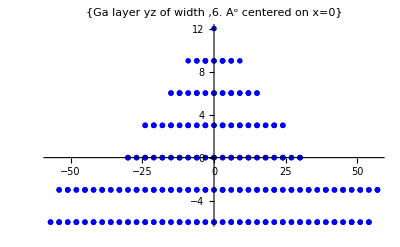

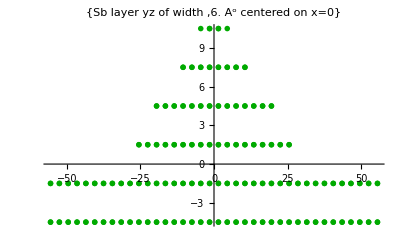

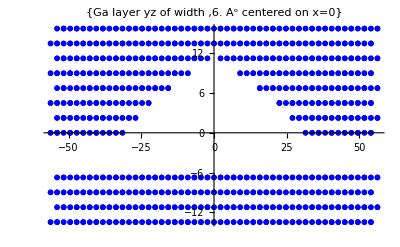

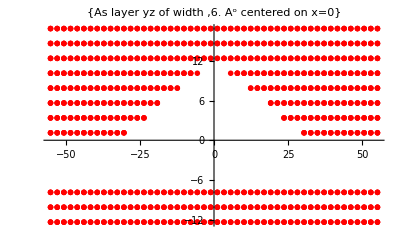

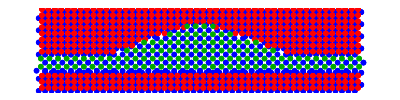

```mathematica
(*Collecting data for graphics 2D*)
YZ=Partition[Flatten[{GAinYZ,SBinYZ,GAoutYZ,ASoutYZ}],2];
w1=ListPlot[GAinYZ,PlotStyle->{PointSize[0.01],Blue},PlotRange->All,PlotLabel->{"Ga layer yz of width ",layer"A^o centered on x=0"}]
w4=ListPlot[SBinYZ,PlotStyle->{PointSize[0.01],Darker[Green]},PlotRange->All,PlotLabel->{"Sb layer yz of width ",layer"A^o centered on x=0"}]
w2=ListPlot[GAoutYZ,PlotStyle->{PointSize[0.01],Blue},PlotRange->All,PlotLabel->{"Ga layer yz of width ",layer"A^o centered on x=0"}]
w3=ListPlot[ASoutYZ,PlotStyle->{PointSize[0.01],Red},PlotRange->All,PlotLabel->{"As layer yz of width ",layer"A^o centered on x=0"}]
Show[w1,w2,w3,w4,PlotRange->All,PlotLabel->{"UNRELAXED Atomic layer yz &x=0 of width ",layer"A^o"}];

w1=ListPlot[GAinYZ,PlotStyle->{PointSize[0.01],Blue},PlotRange->All];
w2=ListPlot[GAoutYZ,PlotStyle->{PointSize[0.01],Blue},PlotRange->All];
Show[w1,w2,w3,w4,PlotRange->All, Axes->False,AspectRatio->1/4]
```

2.6 3D graphs HT+WL

```mathematica
GAinP=ListPointPlot3D[{GAin},PlotStyle->{PointSize[0.01],Blue},BoxRatios->{1, 1, 1}];
SBinP=ListPointPlot3D[{SBin},PlotStyle->{PointSize[0.01],Green},BoxRatios->{1, 1, 1}];
GAoutP=ListPointPlot3D[{GAout},PlotStyle->{PointSize[0.003],Blue},BoxRatios->{1, 1, 1}];
ASoutP=ListPointPlot3D[{ASout},PlotStyle->{PointSize[0.003],Red},BoxRatios->{1, 1, 1}];
```

```mathematica
(*Collecting data for graphics 3D*)
Tor=ParametricPlot3D[{Cos[t] (R0+RQ*Cos[u]),Sin[t] (R0+RQ*Cos[u]),RQ*Sin[u]},{t,0,2 Pi},{u,0, Pi},PlotStyle->Opacity[0.2]];
Plan[x_,y_]:=0;
PLAN=Plot3D[Plan[x,y],{x,-(R0+3/2RQ),(R0+3/2RQ)},{y,-(R0+3/2RQ),(R0+3/2RQ)},PlotStyle->Opacity[0.2],PlotRange->All];

Show[GAinP,SBinP,BoxRatios->{1, 1,1/3},PlotLabel->"GaSb hemitorus+wetting layer",PlotRange->All, Axes->False]
Show[GAoutP,ASoutP,BoxRatios->{1, 1, 1/2},PlotLabel->"GaAs out of hemitorus",PlotRange->All, Axes->False]
Show[GAinP,SBinP,GAoutP,ASoutP,BoxRatios->{1, 1, 1/2},PlotLabel->"UNRELAXED GaSb hemitorus+wetting layer in GaAs",PlotRange->All, Axes->False]
Show[Tor,GAinP,SBinP,BoxRatios->{1, 1,1/3},PlotLabel->"GaSb hemitorus+wetting layer",PlotRange->All]
Show[Tor,PLAN,GAinP,SBinP,GAoutP,ASoutP,BoxRatios->{1, 1, 1/2},PlotLabel->"UNRELAXED GaSb hemitorus+wetting layer in GaAs",PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

2.7 3D graphs Cone+WL

```mathematica
GAinP=ListPointPlot3D[{GAin},PlotStyle->{PointSize[0.01],Blue},BoxRatios->{1, 1, 1}];
SBinP=ListPointPlot3D[{SBin},PlotStyle->{PointSize[0.01],Green},BoxRatios->{1, 1, 1}];
GAoutP=ListPointPlot3D[{GAout},PlotStyle->{PointSize[0.003],Blue},BoxRatios->{1, 1, 1}];
ASoutP=ListPointPlot3D[{ASout},PlotStyle->{PointSize[0.003],Red},BoxRatios->{1, 1, 1}];
```

```mathematica
Show[GAinP,SBinP,BoxRatios->{1, 1,1/3},PlotRange->All, Axes->False]
Show[GAoutP,ASoutP,BoxRatios->{1, 1, 1/2},PlotRange->All, Axes->False]
Show[GAinP,SBinP,GAoutP,ASoutP,BoxRatios->{1, 1, 1/2},PlotRange->All, Axes->False]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-